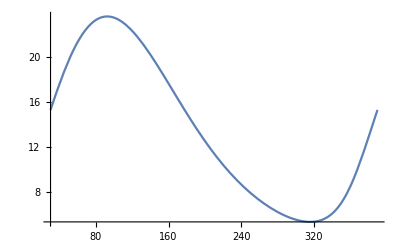

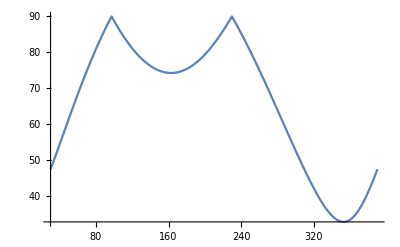

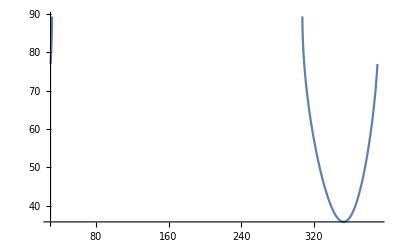

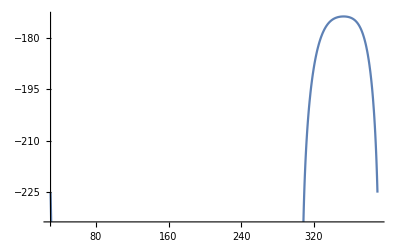

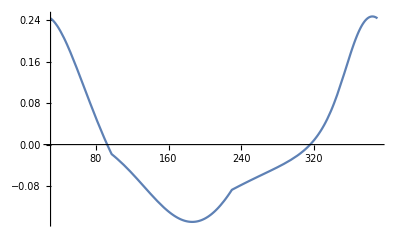

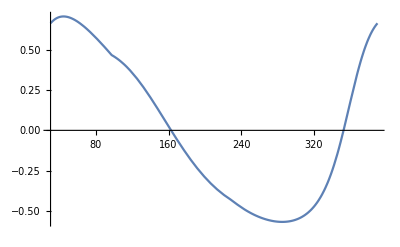

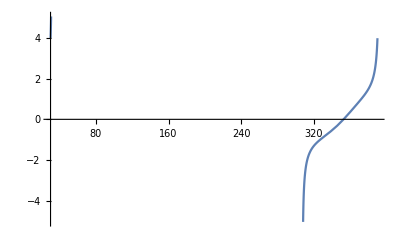

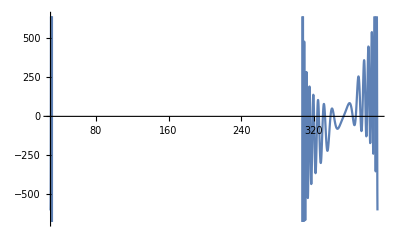

-Graphics-

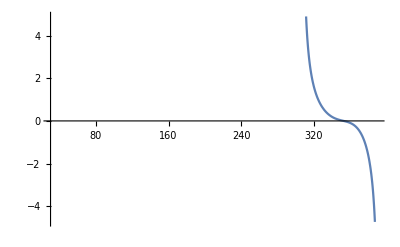

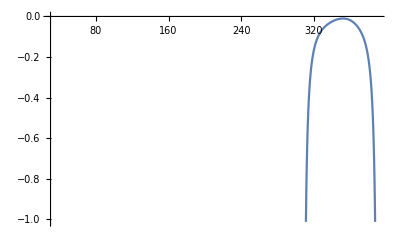

```mathematica
l1=200;
l2=1500;
l4 =400;
l3=1350;
l5=200;
e=(Pi/180);
k=(l4^2)-(l1^2)-(l2^2)-(l3^2)+(2*l3*l1*Cos[u*e]);
a= -(2*l1*l2*Sin[u*e]);
b=(2*l1*l2*Cos[e*u])-(2*l3*l2);
c=2*a*k;
d=((4*(a^2)*(k^2))+(4*(b+k)*(b-k)*((a^2)+(b^2))))^0.5;
f=2*((a^2)+(b^2));
g=ArcSin[((c+d)/f)]*(1/e);
h=(1/e)*ArcSin[((l2*Sin[g*e])-(l1*Sin[u*e]))/l4];
i=(1/e)*ArcSin[((l4*Sin[h*e])-100)/l5];
j=-(l4*Cos[e*h])+(l5*Cos[i*e]);
a1=l1*Sin[u*e];
b1=l2*Sin[g*e];
c1=l4*Sin[h*e];
a2=-l1*Cos[u*e];
b2=l2*Cos[g*e];
c2=l4*Cos[h*e];
m=(((a1*c2)-(a2*c1))*1)/((b2*c1)-(b1*c2));
n=(a1+(b1*m))/c1;
q=(l4*Cos[h*e]*n)/(l5*Cos[i*e]);
s= (l4*Sin[h*e]*n)-(l5*Sin[i]*q);
a3=(l1*Cos[u*e])+(l2*Cos[g*e]*m*m)-(l4*Cos[h*e]*n*n);
b3=l1*Sin[u*e];
c3=l2*Sin[g*e];
d3=l4*Sin[h*e];
a4= (l1*Sin[u*e])-(l2*Sin[g*e]*m*m)+(l4*Sin[h*e]*n*n);
b4=-l1*Cos[u*e];
c4= l2*Cos[g*e];
d4=l4*Cos[h*e];
v=((a4*d3)-(a3*d4))/((c3*d4)-(c4*d3));
w=((c4*v)+a4)/d4;
o=(-(l4*Sin[h*e]*n*n)+(l4*Cos[h*e]*w)+(l5*Sin[i*e]*q*q))/(l5*Cos[i*e]);
p=(l4*Cos(h*e)* n*n)-(l5*Cos[i*e]*q*q)+(l4*Sin[h*e]*w)-(l5*Sin[i*e]*o);
Plot[g, {u,30,390}]
Plot[h, {u,30,390}]
Plot[i, {u,30,390}]
Plot[j, {u,30,390}]
Plot[m, {u,30,390}]
Plot[n, {u,30,390}]
Plot[q, {u,30,390}]
Plot[s, {u,30,390}]
Plot[v, {u,30,390}]
Plot[w, {u,30,390}]
Plot[o, {u,30,390}]
Plot[p, {u,30,390}]
w1=D[j,u];
Plot[w1, {u,30,390}]
w2=D[w1,u];
Plot[w2, {u,30,390}]




The following 8 graphs are the graphs of (Theta2vsTheta1),(Theta4vsTheta1),(Theta5vsTheta1),(x vsTheta1),(omega2vsTheta1),(omega4vsTheta1),(omega5vsTheta1),(Vel.x  vsTheta1),(Alpha2vsTheta1),(Alpha4vsTheta1),(Alpha5vsTheta1),(Acc.x  vsTheta1):
```